```mathematica
(***************************************)
(****Scalar field equaition*************)
(***************************************)
(***************************************)
(***************Background In case!****************)
(***************************************)
(*The difference here is we do not multiply to Η[a]π we have instead H[1]π so does not change in time!*)
w=-0.9;
cs=10^-3;
(*H0=0.00022593979933110373*) c=2997.92458 100;
H0=100 h/c;
h=0.67556;
Omegab=0.022032/h/h;Omegacdm=0.12038/h/h;
Omegam=Omegab+Omegacdm;OmegaLambda=0.0;
Omegarad=9.16681 10^-5;Omegakessence=1.-Omegam-Omegarad;
Hubb[a_]:=H0 a √(Omegam a^-3+Omegarad  a^-4+OmegaLambda+Omegakessence a^(-3*(1+w)));
LogLogPlot[Hubb[a],{a,1./(1.+100),1}];
SetDirectory[NotebookDirectory[]];
(*Eq1II=3 cs^2( H[τ]^2-H'[τ]) piC[τ]-3 H[τ] (w ζ[τ]+cs^2 Ψ[τ]) +ζ'[τ]-3 cs^2 Φ'[τ]+cs^2 kwave^2 piC[τ];
Eq2II= piC'[τ]- ζ[τ]+H[τ]piC[τ]-Ψ[τ];*)
(*Trivial equation:*)
Eq1II= 3 cs^2(  H[τ]^2) piC[τ] +ζ'[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
(*Solving the field only equation*)
Ψ[τ]=0;
 Φ'[τ]=0;
Eq1I=Eq1II/.{piC->(piC[a[#]]&),ζ->(ζ[a[#]]&) };
Eq2I=Eq2II/.{piC->(piC[a[#]]&),ζ->(ζ[a[#]]&) };
a''[τ]=a[τ](H[τ]^2+H'[τ]);
a'[τ]=a[τ]H[τ];
H[τ_]:=Hubb[a[τ]];
(*Field equation in terms of scale factor!*)
Eq1:=Eq1I/.a[τ]:>a;
Eq2:=Eq2I/.a[τ]:>a;
```

```mathematica
(***************************************)
(***************IC read fromt the file***)
(***************************************)
(*Class file columns: # 1:k (h/Mpc) 2:d_kess_pi 3:t_kess_zeta 4:delta_fld 5:theta_fld 6:psi 7:delta_cdm 8:H_conf/H0 *)
data=Import["./Class_files/Class_kess_cs_e3_z100_newt_Gev.dat",{"Data",{All}}];

(*Making output file foe Gev field!*)
As=2.215 10^-9;
h=0.67556;
kp=0.05/h;
ns=0.9619;
cs2=10^-6;
Addr="2018.05.23.14.59.52";
(*IMPORTS*)
dataGevphiz100=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_000_phi.dat",{"Data",{All}}],{_?NumberQ,___}];
dataGevphiprimez100=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_000_phi_prime.dat",{"Data",{All}}],{_?NumberQ,___}];
datazetaGev100=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_000_zeta.dat",{"Data",{All}}],{_?NumberQ,___}];
datapiGev100=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_000_pi_k.dat",{"Data",{All}}],{_?NumberQ,___}];
datapiGev10=
Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_002_pi_k.dat",{"Data",{All}}],{_?NumberQ,___}];
datazetaGev10=Cases[Import["./NewVariable_Gevolution/"<> Addr<>"/kess_pk_cs_e3_002_zeta.dat",{"Data",{All}}],{_?NumberQ,___}];
(*z=10*)
(*dataGevphiprimez10=Import["./NewVariable_Gevolution/output_1_128/kess_pk_cs_e3_004_phi_prime_z10.dat",{"Data",{All}}]*)
(*dataGevphiz10=Import["./NewVariable_Gevolution/output_1_128/kess_pk_cs_e3_004_phi_z10.dat",{"Data",{All}}];*)
```

```mathematica
GevFieldz100=√(datapiGev100[[All,2]]/(As (datapiGev100[[All,1]]/kp)^(ns-1)));

Gevzetaz100=√(datazetaGev100[[All,2]]/(As (datazetaGev100[[All,1]]/kp)^(ns-1)));

Gevphiprimez100=√(dataGevphiprimez100[[All,2]]/(As (dataGevphiprimez100[[All,1]]/kp)^(ns-1)));
Gevphiz100=√(dataGevphiz100[[All,2]]/(As (dataGevphiz100[[All,1]]/kp)^(ns-1)));
a0=1./(1.+99.597220);
a1=1./(1.+9.951253);
Δa=0.0001; (*Sampling to solve ODE*)
Agrex=Table[Table[0,{aa,1,Floor[((a1-a0)/Δa)]+1},{num,1,3}],{k,1,Dimensions[datapiGev100[[All,1]]][[1]]}];
Dimensions[Agrex];(*k , a , pi[a], zeta[a]*)(*For each k we have a * 3 where a is the number of a sampling and 3 is the number of columns. a pi and pi' for  *)
(*Agrex[[4]] //MatrixForm*)
(*phiprimez10=√(dataGevphiprimez10[[All,2]]/(As (dataGevphiprimez10[[All,1]]/kp)^(ns-1)));
Gevphiz10=√(dataGevphiz10[[All,2]]/(As (dataGevphiz10[[All,1]]/kp)^(ns-1)));*)
GevFieldz10=√(datapiGev10[[All,2]]/(As (datapiGev10[[All,1]]/kp)^(ns-1)));
(*Gevpivz100=√(datapivGev100[[All,2]]/(As (datapivGev100[[All,1]]/kp)^(ns-1)));*)
Gevzetaz10=√(datazetaGev10[[All,2]]/(As (datazetaGev10[[All,1]]/kp)^(ns-1)));
(***************************************)
(****For each k in IC file we need to solve th e ODE numerically!***************)
(***************************************)
kmax=Dimensions[datapiGev100[[All,1]]][[1]];
amaxComun=Floor[((a1-a0)/Δa)]+1;
GevPowerDataz100=Table[{datapiGev100[[l,1]],GevFieldz100[[l]],Gevzetaz100[[l]]},{l,1,Dimensions[GevFieldz100][[1]]}];
GevPowerDataz10=Table[{datapiGev10[[l,1]],GevFieldz10[[l]],Gevzetaz10[[l]]},{l,1,Dimensions[GevFieldz10][[1]]}];

For[kk=1,kk<kmax+1,kk++,
(*k is wavenumber in the eq
The IC is set for each wavenumber accordingly!
Also \Psi is set for each k accordingly in the loop which is assumed to be constant in matter dominated universe!*)
kwave=GevPowerDataz100[[kk,1]]*h;
(*We multiply by h since the unit of k is 1/Mpc not h/Mpc! while in the file is k=[h/Mpc] *)
(*piC'[a0]==data[[kk,3]]/(Hubb[a0]a0) is IC for dπ/da*)
(*Ψ[τ]=Gevphiz100[[kk]];*)
(*Φ'[τ]=Gevphiprimez100[[kk]]Hubb[a0];*)
Ψ[τ]=0;
Φ'[τ]=0;
(*It is multiplied to Hubble since it is function of τ while after changing the variable it gets H factor*)
(*Φprime must be provided in new variable a[tau]*)
(*Φprime=Gevphiprimez21[[kk]]Hubb[a0];*)
Sol=NDSolve[{Eq1==0,Eq2==0,piC[a0]==GevPowerDataz100[[kk,2]]/Hubb[a0],ζ[a0]==GevPowerDataz100[[kk,3]]},{piC,ζ},{a,a0,a1}];  (*The pi field in Gevolution is divided by H since in the output it is multiplied to!*)(*Note that for the initial value of π'[a0] it is not just data[[kk,3]]/(Hubb[a0]a0) since now it is the function of "a" which gets a new coefficient by changing the variable but not for ζ which is dimensionless*)
Agrex[[kk]][[All,1]]=Table[a,{a,a0,a1,Δa}];
(*Hubb[a]piC[a] is dimensionless field,  piC'[a]Hubb[a]a is dπ/dτ according to chain rule!*)
Agrex[[kk]][[All,{2,3}]]=Table[{Hubb[a]piC[a]/.Sol, ζ [a]/.Sol},{a,a0,a1,Δa}]; (*Hubb[a]piC[a] is a dimensionless variable and ζ [a]Hubb[a]a is to change in temrs of conformal time*)
]
Agrex[[3]][[{2,7},2]]//MatrixForm; (*To check consistency!*)
(*K info is in the loaded file, and for each k we have the solution in time (pi, pi')!*)
(*Ψdata[[i,1]] is k lists! Agrex[[i]][[2,2]][[1]] is pi soluition for constant time!*)
```

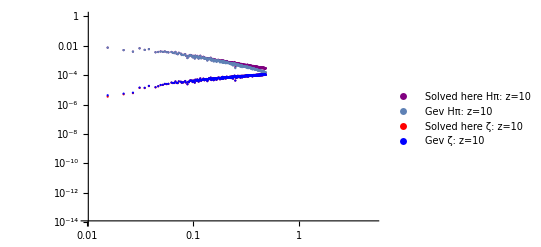

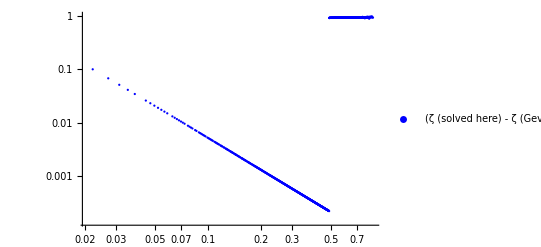

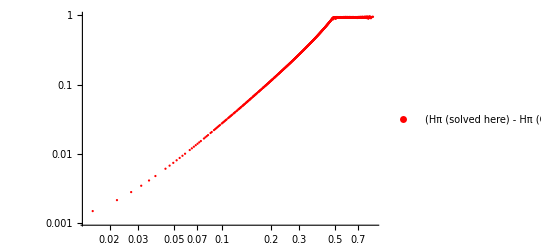

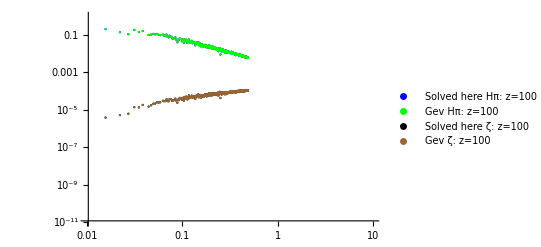

```mathematica
MatSolz100=Table[{GevPowerDataz100[[k,1]],Abs[Agrex[[k]][[1,2]][[1]]],Abs[Agrex[[k]][[1,3]][[1]]]},{k,1,kmax}];
MatSolz10=Table[{GevPowerDataz10[[k,1]],Abs[Agrex[[k]][[amaxComun,2]][[1]]],Abs[Agrex[[k]][[amaxComun,3]][[1]]]},{k,1,kmax}]//N;
dataz10=
Import["./Class_files/Class_kess_cs_e3_z10_newt_Gev.dat",{"Data",{All}}];
Errorπ100=Table[{MatSolz100[[k,1]],Abs[(MatSolz100[[k,2]]-GevPowerDataz100[[k,2]])]/GevPowerDataz100[[k,2]]},{k,1,kmax}]//N;
Errorζ100=Table[{MatSolz100[[k,1]],Abs[(MatSolz100[[k,3]]-GevPowerDataz100[[k,3]])]/GevPowerDataz100[[k,3]]},{k,2,kmax}]//N;
Errorζ10=Table[{MatSolz10[[kl,1]],Abs[(MatSolz10[[kl,3]]-GevPowerDataz10[[kl,3]])]/GevPowerDataz10[[kl,3]]},{kl,2,kmax}]//N;
Errorπ10=Table[{MatSolz10[[km,1]],Abs[(MatSolz10[[km,2]]-GevPowerDataz10[[km,2]])]/GevPowerDataz10[[km,2]]},{km,1,kmax}]//N;

pπ100=ListLogLogPlot[MatSolz100[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{"Solved here Ηπ: z=100"},ImageSize->400,PlotRange->{{10^-2,10},{10^-11,10^0}}];
pπ10=ListLogLogPlot[MatSolz10[[All,{1,2}]],PlotStyle->{Purple,Line,PointSize[0.004]},ImageSize->400,PlotLegends->{"Solved here Ηπ: z=10"},PlotRange->{{10^-2,5},{10^-14,10^0}}];
pζ100=ListLogLogPlot[MatSolz100[[All,{1,3}]],PlotStyle->{Black,Line,PointSize[0.004]},PlotLegends->{"Solved here ζ: z=100"},ImageSize->900,PlotRange->{{10^-2,10},{10^-12,10^-2}}];
pζ10=ListLogLogPlot[MatSolz10[[All,{1,3}]],PlotStyle->{Red,Line,PointSize[0.004]},ImageSize->900,PlotLegends->{"Solved here ζ: z=10"},PlotRange->{{10^-2,5},{10^-12,10^-6}}];
(*p1=ListLogLogPlot[MatSolz100[[All,{1,2}]],PlotStyle->{Green,Line,PointSize[0.004]},PlotLegends->{"Solved here π: z=100"},ImageSize->400,PlotRange->{{10^-4,10},{10^-6,1}}];*)
pπGev100=ListLogLogPlot[GevPowerDataz100[[All,{1,2}]],PlotStyle->{Green,Line,PointSize[0.004]},PlotLegends->{"Gev Ηπ: z=100"},ImageSize->400];
pπGev10=ListLogLogPlot[GevPowerDataz10[[All,{1,2}]],PlotStyle->{Maroon,Line,PointSize[0.004]},PlotLegends->{"Gev Ηπ: z=10"},ImageSize->400];
pζGev100=ListLogLogPlot[GevPowerDataz100[[All,{1,3}]],PlotStyle->{Brown,Line,PointSize[0.004]},PlotLegends->{"Gev ζ: z=100"},ImageSize->600];
pζGev10=ListLogLogPlot[GevPowerDataz10[[All,{1,3}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{"Gev ζ: z=10"},ImageSize->600];
(*Errors:*)
perrorζ100=ListLogLinearPlot[Errorζ100[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{" ζ  rel error: z=100"},ImageSize->600];
perrorπ100=ListLogLinearPlot[Errorπ100[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},PlotLegends->{" Ηπ rel error: z=100"},ImageSize->600];
perrorζ10=ListLogLogPlot[Errorζ10[[All,{1,2}]],PlotStyle->{Blue,Line,PointSize[0.004]},PlotLegends->{" (ζ (solved here) - ζ (Gev ))/(ζ (Gev))  z=10"},ImageSize->400];
perrorπ10=ListLogLogPlot[Errorπ10[[All,{1,2}]],PlotStyle->{Red,Line,PointSize[0.004]},PlotLegends->{" (Ηπ (solved here) - Ηπ (Gev ))/(Ηπ (Gev))  z=10"},ImageSize->400];
(*z=10, Gev and solved here*)
Show[pπ10,pπGev10,pζ10,pζGev10]
(*Relative error between here and Gevolution, z=10, z*)
Show[perrorζ10]
Show[perrorπ10]
(*z=100, Gev and solved here*)

Show[pπ100,pπGev100,pζ100,pζGev100]
(*Relative error between here and Gevolution*)
(*Show[perrorζ100,pζGev100]*)
```

Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ]; Eq1II= 3 cs^2( H[τ]^2) piC[τ] +ζ'[τ];
tiling factor = 16  , nKe_numsteps=20, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 128 , Courant factor  = 48.0
time step limit     = 0.04

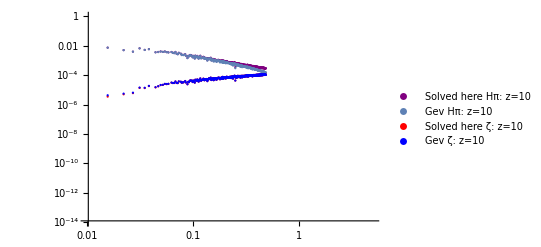

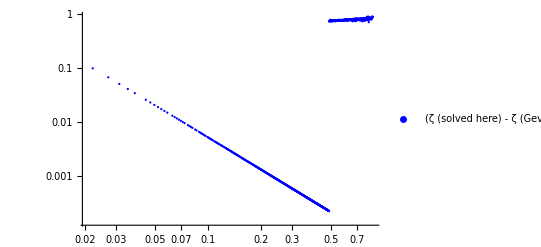

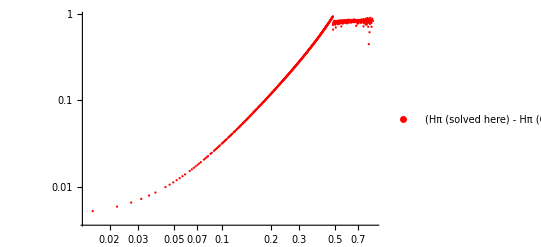

Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ]; Eq1II= 3 cs^2( H[τ]^2) piC[τ] +ζ'[τ];
tiling factor = 32  , nKe_numsteps=10, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 128 , Courant factor  = 48.0
time step limit     = 0.04 , Nothing changes in the low wavenumbers!
For the Euler method, increasing the number of grid we need to increase kessence update enough to get the reasonable results.

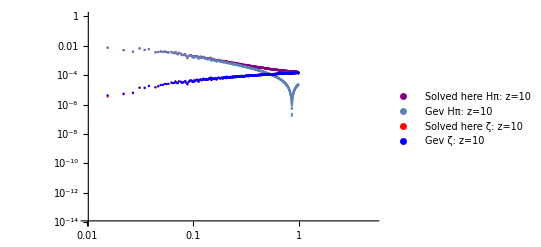

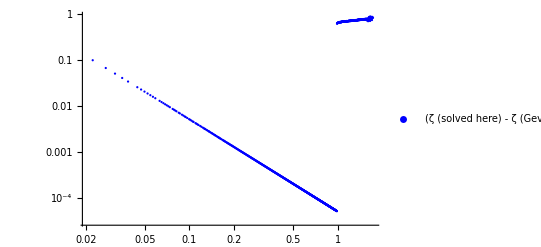

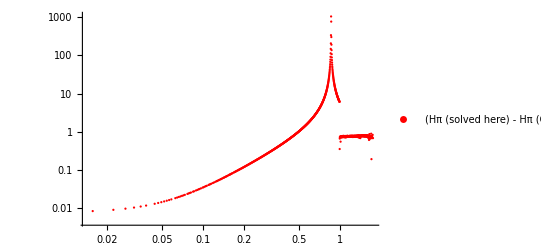

Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ]; Eq1II= 3 cs^2( H[τ]^2) piC[τ]+ζ'[τ];
tiling factor = 16  , nKe_numsteps=20, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04 , Nothing changes in the low wavenumbers!

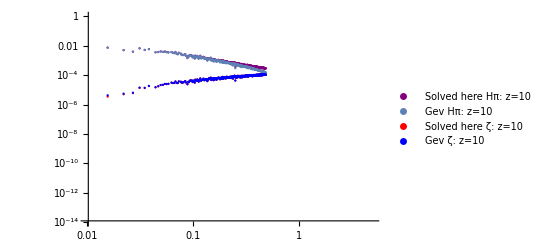

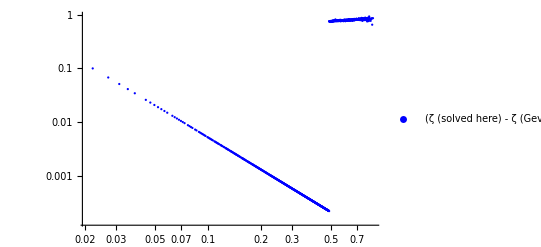

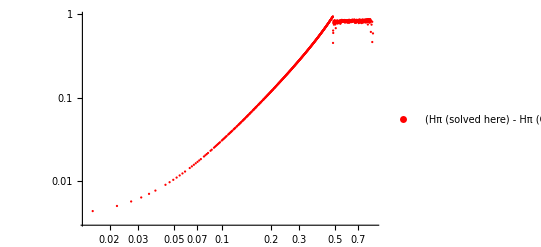

Eq1II= 3 cs^2( H[τ]^2) piC[τ] +ζ'[τ];Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 16  , nKe_numsteps=10, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04

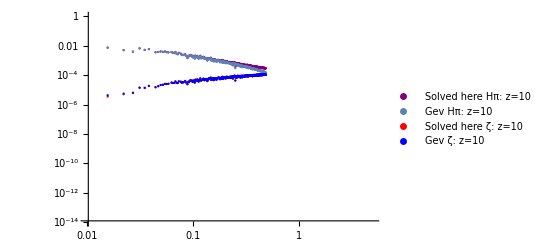

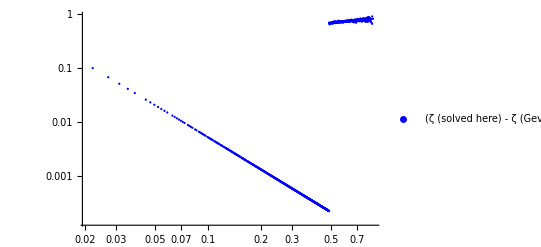

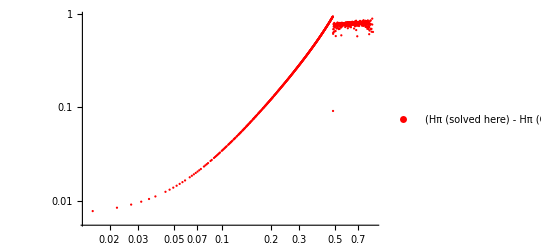

Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ]; Eq1II= 3 cs^2( H[τ]^2-H'[τ]) piC[τ]-3 H[τ] (w ζ[τ]) +ζ'[τ];
tiling factor = 16  , nKe_numsteps=40, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04

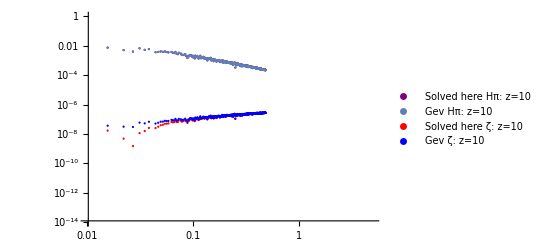

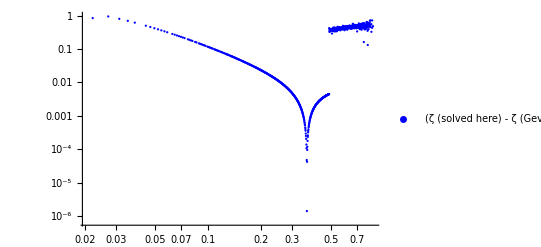

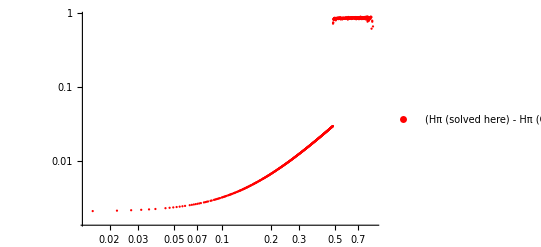

Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ]; Eq1II= 3 cs^2( H[τ]^2-H'[τ]) piC[τ]-3 H[τ] (w ζ[τ]) +ζ'[τ];
tiling factor = 16  , nKe_numsteps=20, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04

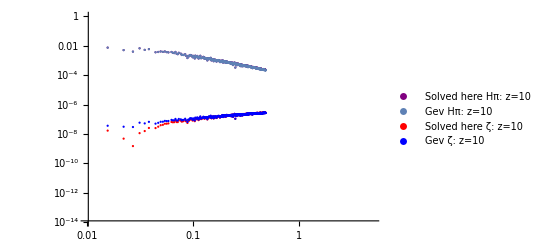

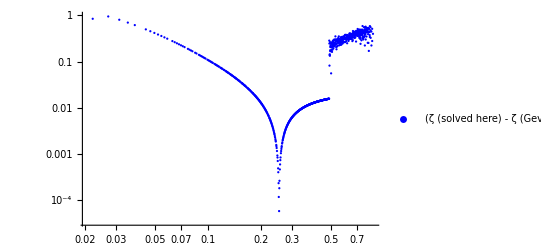

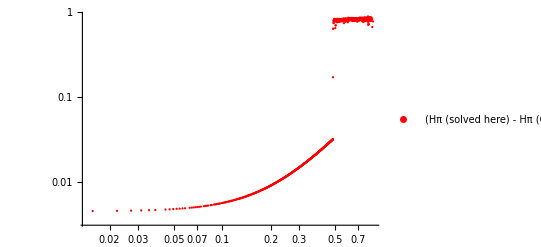

Eq1II= 3 cs^2( H[τ]^2-H'[τ]) piC[τ]-3 H[τ] (w ζ[τ]+cs^2 Ψ[τ]) +ζ'[τ]-3 cs^2 Φ'[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 32  , nKe_numsteps=10, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 128 , Courant factor  = 48.0
time step limit     = 0.02

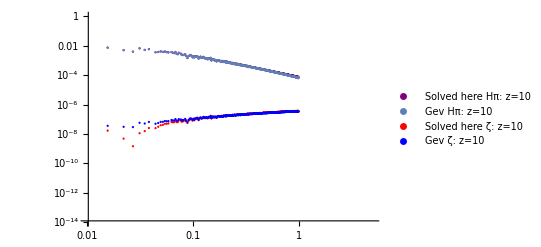

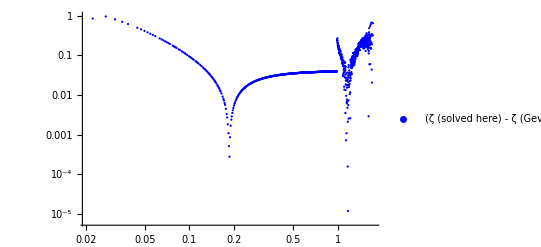

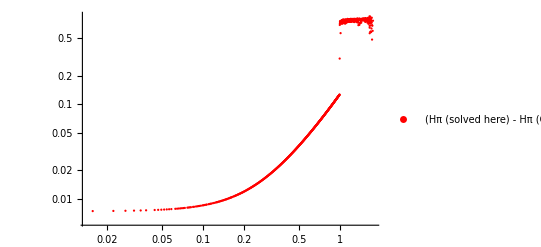

Eq1II= 3 cs^2( H[τ]^2-H'[τ]) piC[τ]-3 H[τ] (w ζ[τ]+cs^2 Ψ[τ]) +ζ'[τ]-3 cs^2 Φ'[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 16  , nKe_numsteps=5, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04

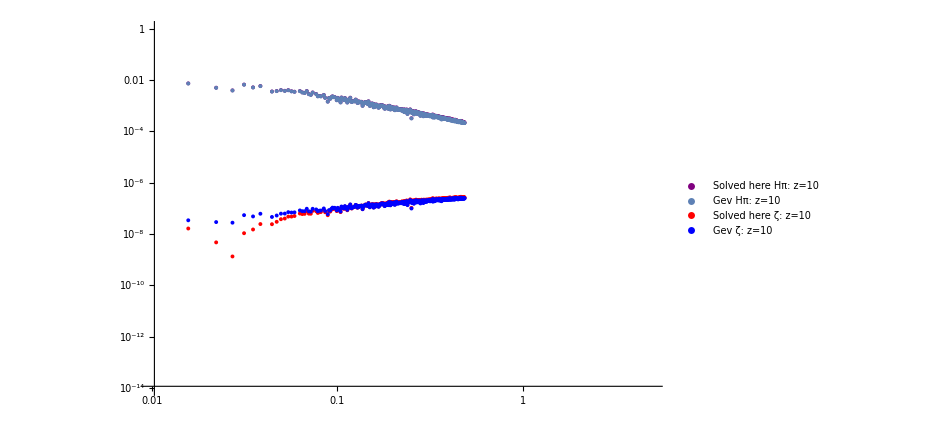

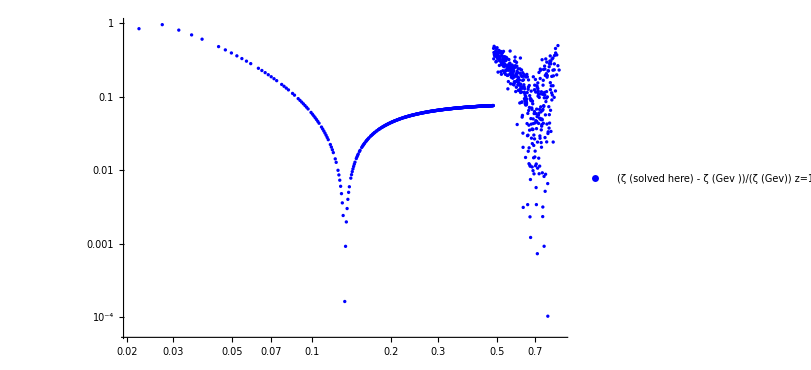

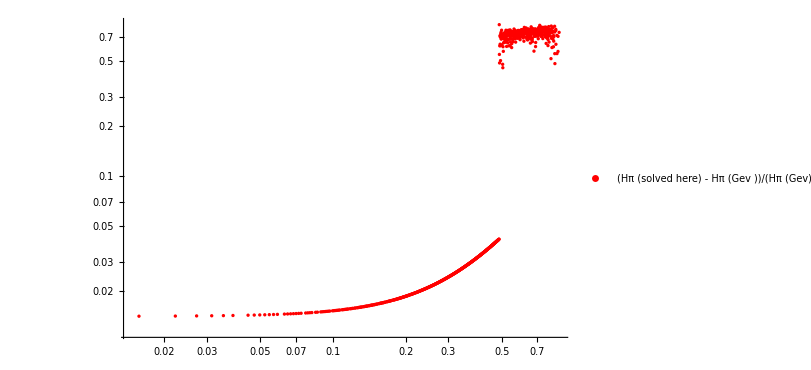

Eq1II= 3 cs^2( H[τ]^2-H'[τ]) piC[τ]-3 H[τ] (w ζ[τ]+cs^2 Ψ[τ]) +ζ'[τ]-3 cs^2 Φ'[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 16  , nKe_numsteps=1, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04

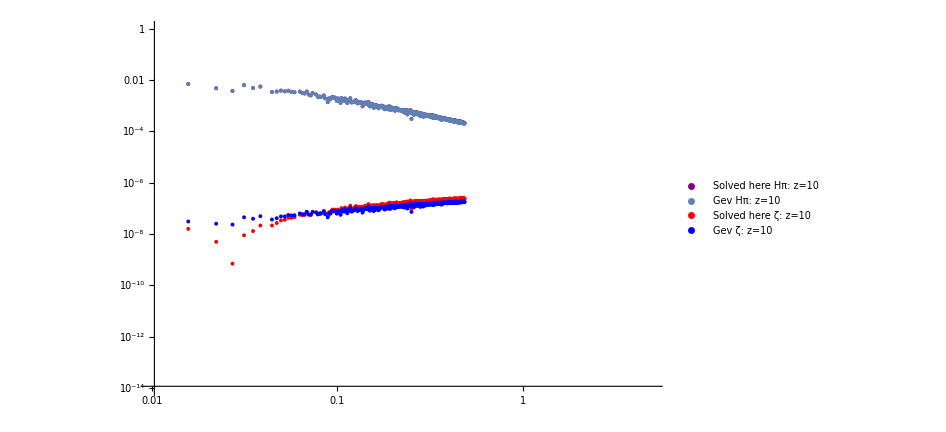

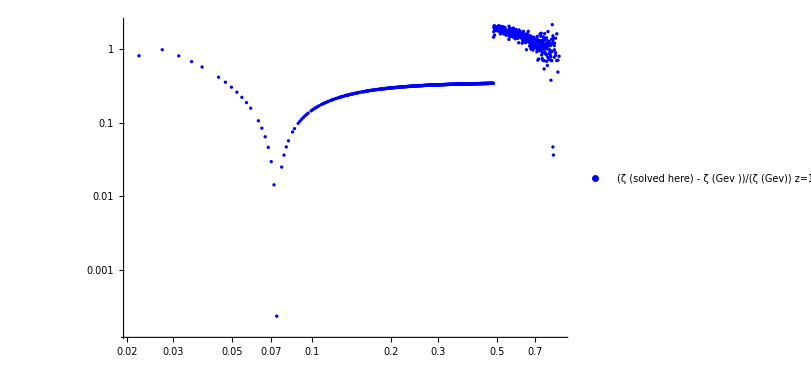

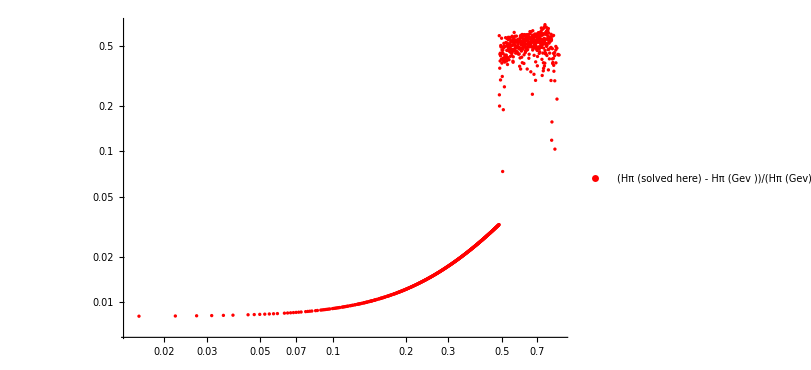

Eq1II= +ζ'[τ]+cs^2 kwave^2 piC[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 64  , nKe_numsteps=10, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 256 , Courant factor  = 48.0
time step limit     = 0.04

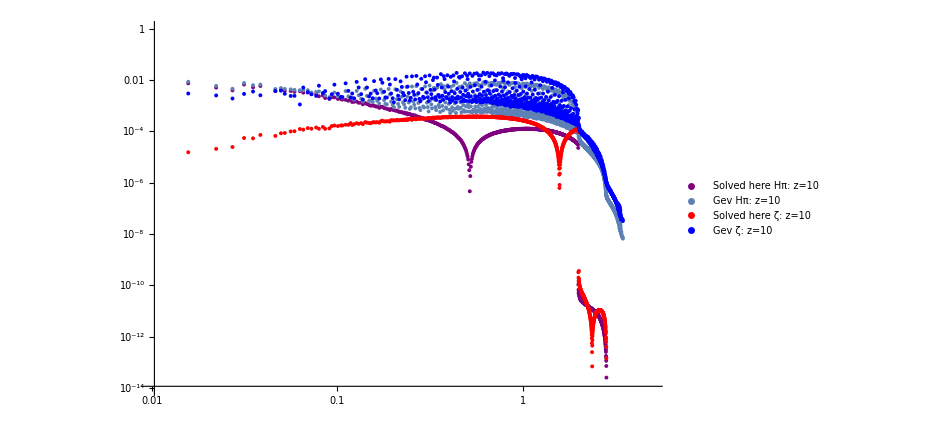

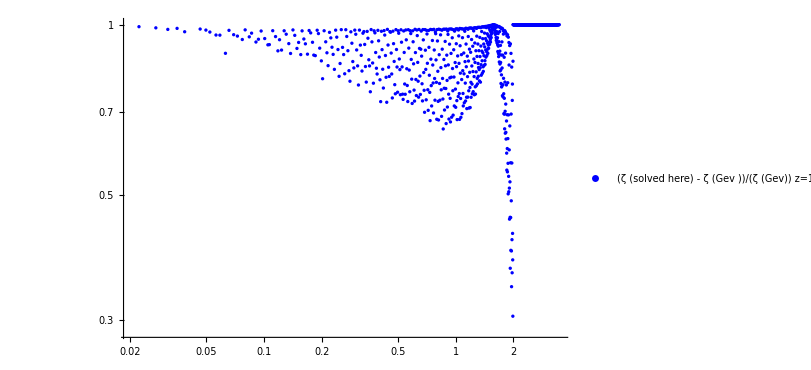

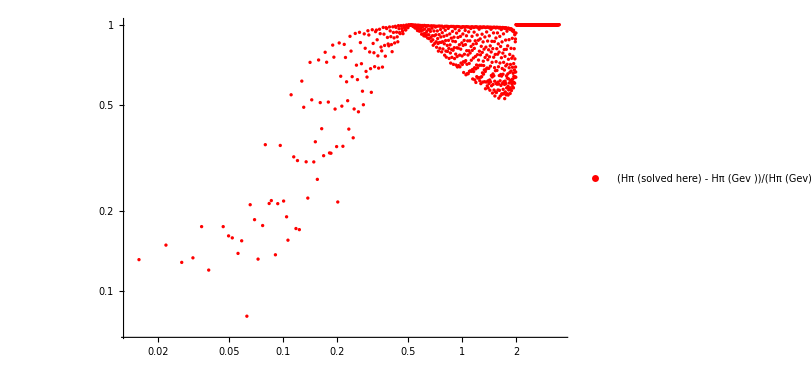

Eq1II= +ζ'[τ]+cs^2 kwave^2 piC[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 32  , nKe_numsteps=10, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 128 , Courant factor  = 48.0
time step limit     = 0.04

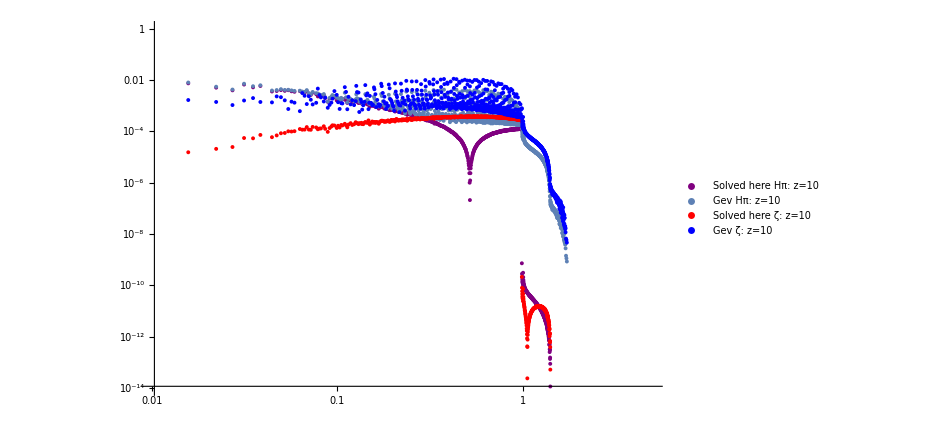

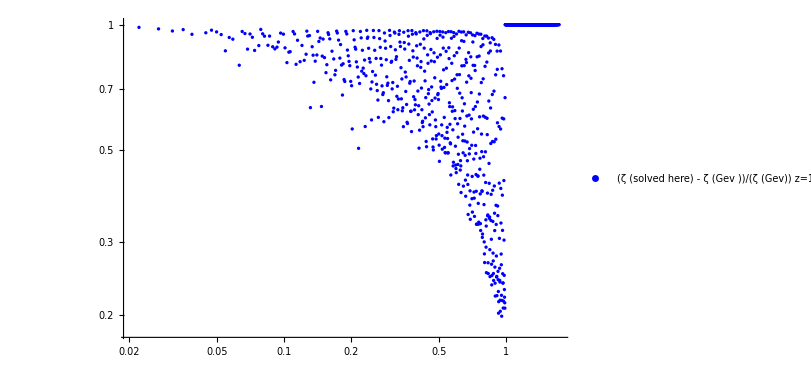

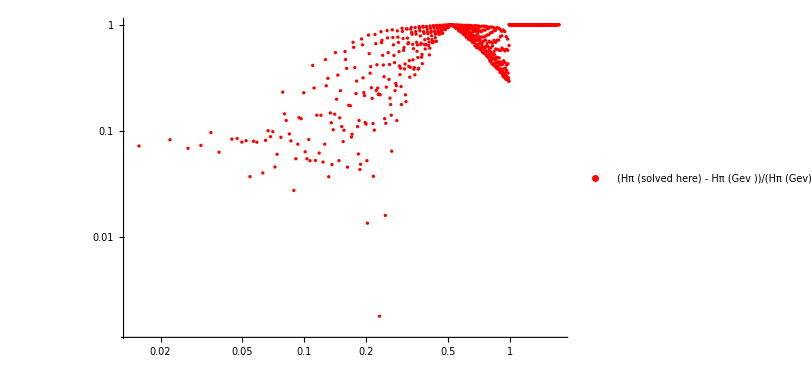

Eq1II= +ζ'[τ]+cs^2 kwave^2 piC[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 16  , nKe_numsteps=20, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04

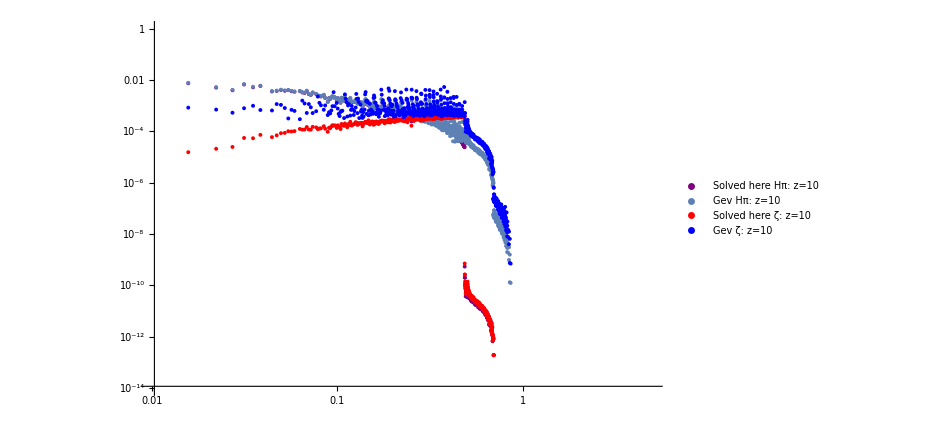

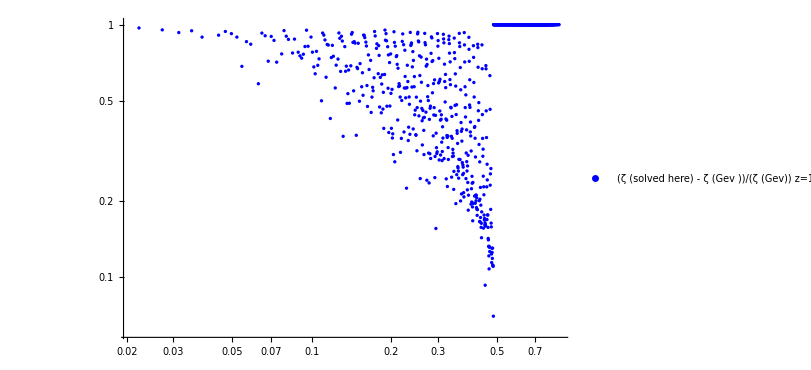

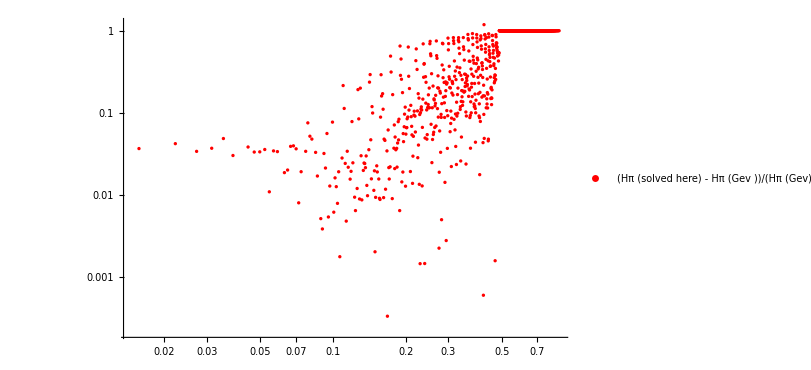

Eq1II= +ζ'[τ]+cs^2 kwave^2 piC[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 16  , nKe_numsteps=10, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04

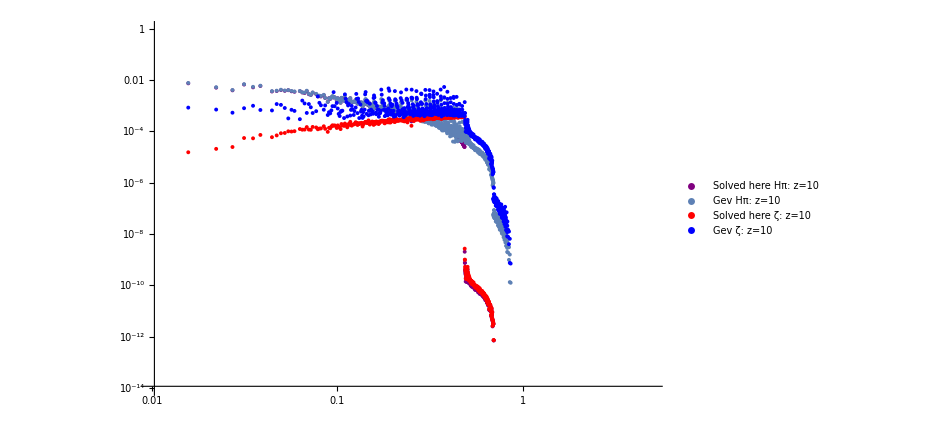

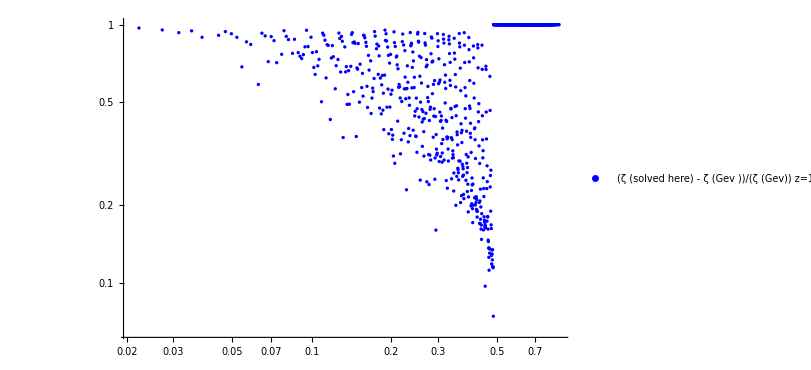

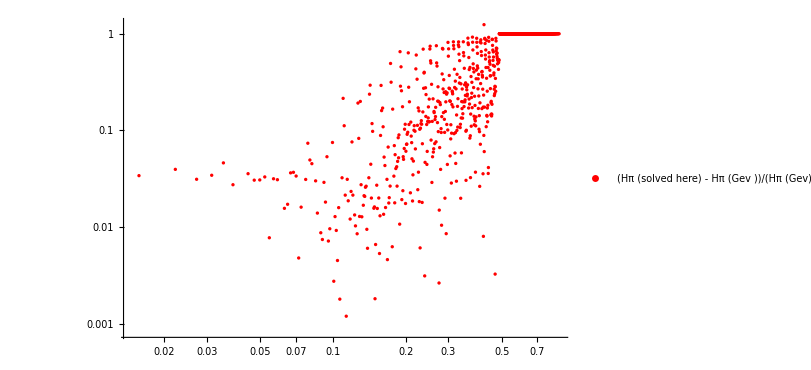

Eq1II= +ζ'[τ]+cs^2 kwave^2 piC[τ]-3 H[τ] w ζ[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 64  , nKe_numsteps=10,  Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 256 , Courant factor  = 48.0
time step limit     = 0.04

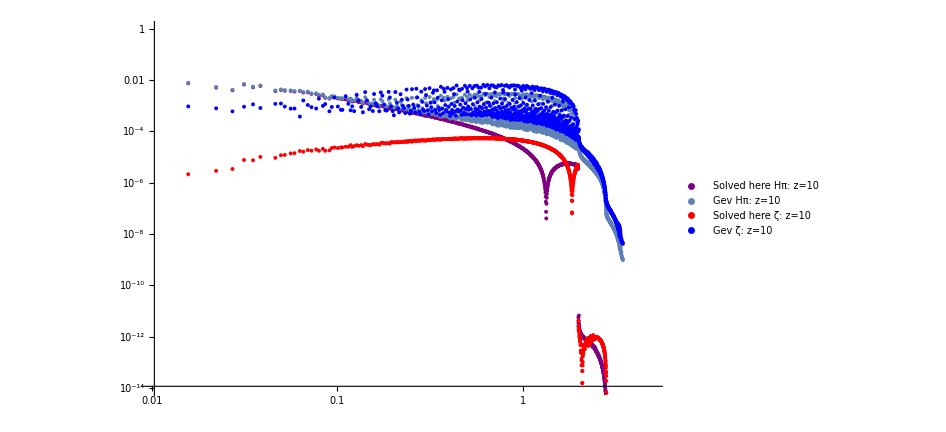

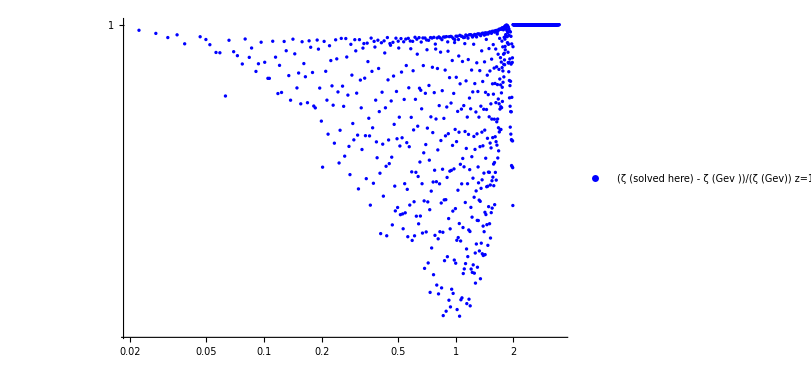

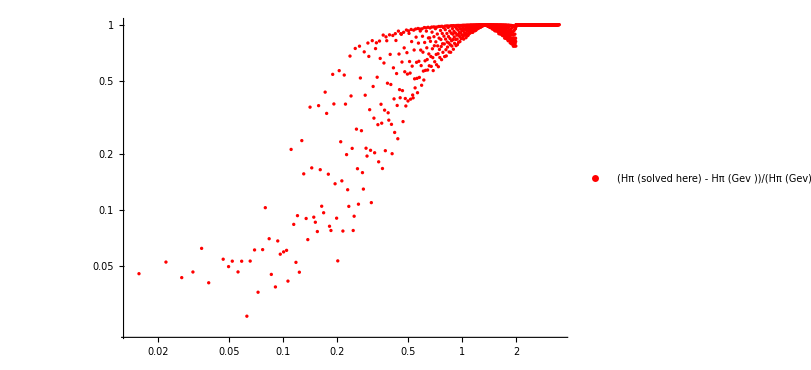

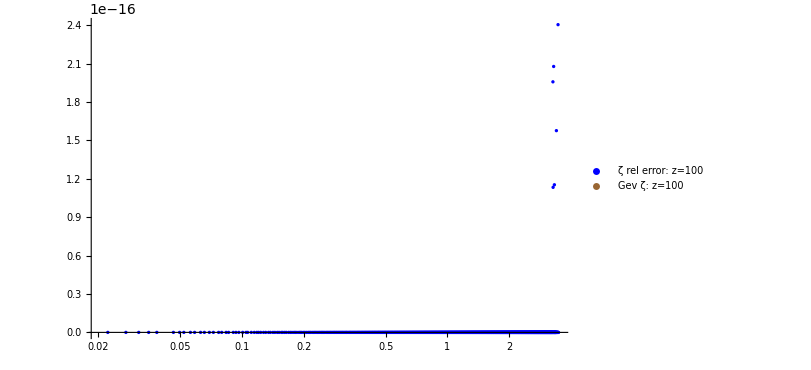

Eq1II= +ζ'[τ]+cs^2 kwave^2 piC[τ]-3 H[τ] w ζ[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 32  , nKe_numsteps=10,  Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 128 , Courant factor  = 48.0
time step limit     = 0.04

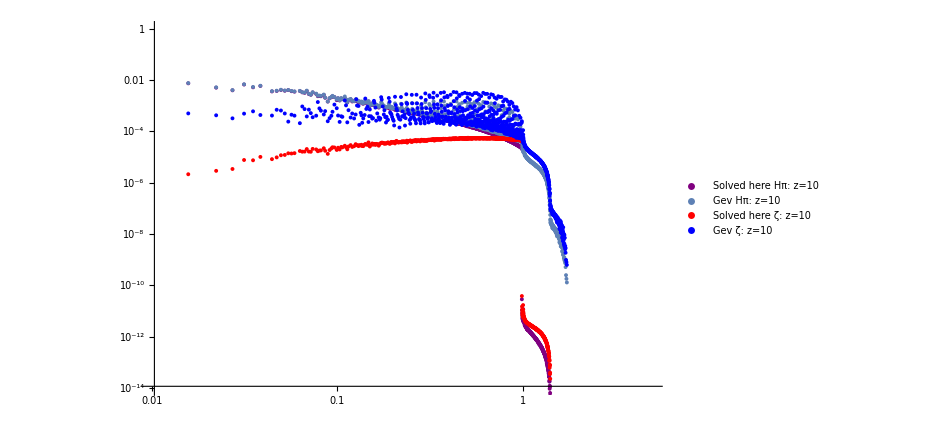

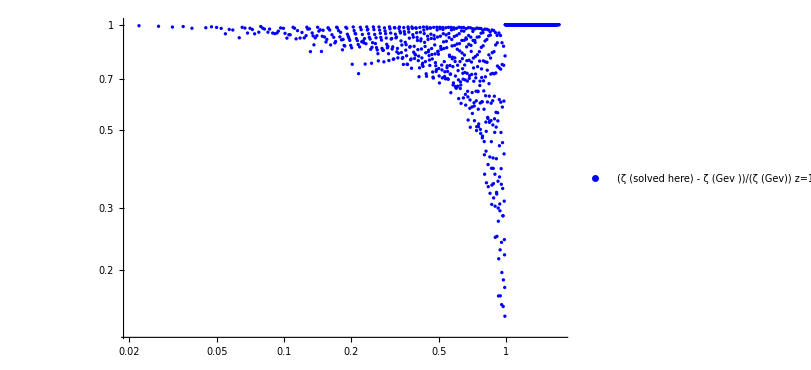

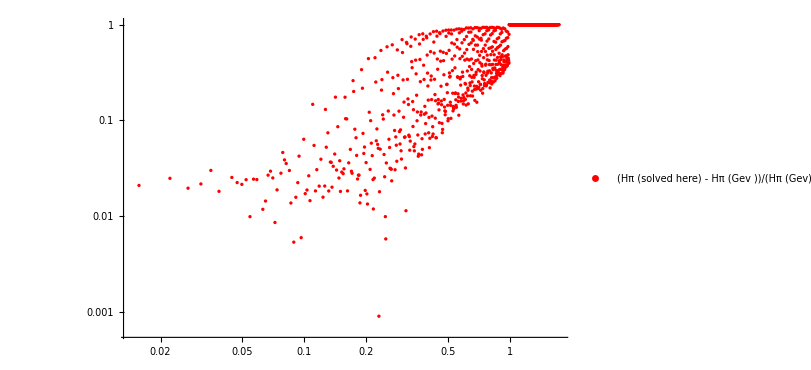

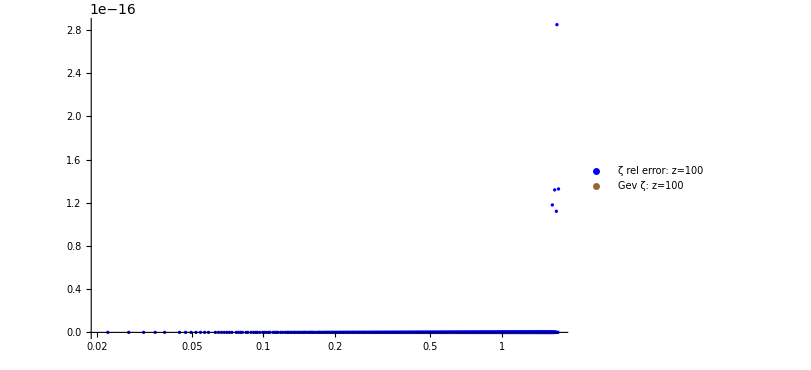

Eq1II= +ζ'[τ]+cs^2 kwave^2 piC[τ]-3 H[τ] w ζ[τ];
Eq2II= piC'[τ]+H[τ]piC[τ]- ζ[τ];
tiling factor = 16  , nKe_numsteps=5, Kessence source gravity= 0  , initial redshift    = 100.0, boxsize  = 400.0   , Ngrid = 64 , Courant factor  = 48.0
time step limit     = 0.04